# Homework #11 Andrew Turner

## Problem #1:

### (a) Find the solution(s) of 2 cosh(x/4) - x = 0.

```mathematica
Solve[2*cosh(x/4)-x==0,x]
```

{{x→0}}

### (b) Plot Legendre polynomial for n=1,2,3,4

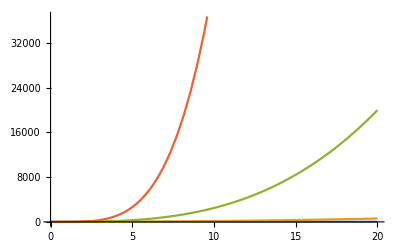

```mathematica
Plot[Evaluate[Table[LegendreP[n,x],{n, 4}]], {x, 0, 20}]
```

### (c) Find the zeroes of these functions

```mathematica
a = Table[LegendreP[n,x] == 0, {n,4}]
```

{x==0,1/2 (-1+3 x^2)==0,1/2 (-3 x+5 x^3)==0,1/8 (3-30 x^2+35 x^4)==0}

```mathematica
Solve[a[[1]],{x}]
```

{{x→0}}

```mathematica
Solve[a[[2]],{x}]
```

{{x→-1/(√3)},{x→1/(√3)}}

```mathematica
Solve[a[[3]],{x}]
```

{{x→0},{x→-√(3/5)},{x→√(3/5)}}

```mathematica
Solve[a[[4]],{x}]
```

{{x→-√(1/35 (15-2 √30))},{x→√(1/35 (15-2 √30))},{x→-√(1/35 (15+2 √30))},{x→√(1/35 (15+2 √30))}}

## Problem #2:

### (a) Find a general solution to the differential equation du/dt = 2u - 1:

```mathematica
DSolve[u'[t] == 2u[t]-1, u[t], t ]
```

{{u[t]→1/2+ⅇ^(2 t) C[1]}}

### (b) Find a general solution with boundary condition, u(0) = u_0.

```mathematica
DSolve[{u'[t] == 2u[t]-1, u[0]==u0}, u[t], t ]
```

{{u[t]→1/2 (1-ⅇ^(2 t)+2 ⅇ^(2 t) u0)}}

## Problem #3:

### (a) Make a table of the 3 Pauli Matrices in Matrix form:

```mathematica
a =Table[PauliMatrix[k]//MatrixForm, {k,3}]
```

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

### (b) Find eigenvalues and eigenvectors for these matrices:

```mathematica
Eigenvalues[PauliMatrix[1]]
```

{-1,1}

```mathematica
Eigenvectors[PauliMatrix[1]]
```

{{-1,1},{1,1}}

```mathematica
Eigenvalues[PauliMatrix[2]]
```

{-1,1}

```mathematica
Eigenvectors[PauliMatrix[2]]
```

{{ⅈ,1},{-ⅈ,1}}

```mathematica
Eigenvalues[PauliMatrix[3]]
```

{-1,1}

```mathematica
Eigenvectors[PauliMatrix[3]]
```

{{0,1},{1,0}}

### (c) Three equal mass bodies connected by two springs:

```mathematica
U = (k/2) [(x1[t]-x2[t])^2 + (x2[t]-x3[t])^2]
x1''[t] = -k/m(x1[t]- x2[t])
x2''[t] = -k/m (x2[t]-x1[t] + x2[t]-x3[t])
x3''[t] = -k/m (x3[t]-x1[t])
m1 = m2 = m3 = m
k1 = k2 = k
```

Express the right hand side as a matrix.

```mathematica
M =MatrixForm[{{-k/m,k/m,0},{k/m, -2k/m, k/m},{0, k/m, -k/m}}]
```

(-k/m | k/m | 0
k/m | -(2 k)/m | k/m
0 | k/m | -k/m)

```mathematica
X = MatrixForm[{x1, x2, x3}]
```

(x1
x2
x3)

```mathematica
M*X
```

(x1
x2
x3) (-k/m | k/m | 0
k/m | -(2 k)/m | k/m
0 | k/m | -k/m)

```mathematica
M
```

(-k/m | k/m | 0
k/m | -(2 k)/m | k/m
0 | k/m | -k/m)

```mathematica
Eigenvectors[{{-k/m,k/m,0},{k/m,-(2 k)/m,k/m},{0,k/m,-k/m}}]
```

{{1,-2,1},{-1,0,1},{1,1,1}}

```mathematica
Eigenvalues[{{-k/m,k/m,0},{k/m,-(2 k)/m,k/m},{0,k/m,-k/m}}]
```

{-(3 k)/m,-k/m,0}

The first normal mode, (1, -2, 1), describes a motion in which the first and third masses are moving in the same direction while the middle mass is moving twice as fast in the opposite direction. The second normal mode describes a situation where the middle mass is not moving and the end masses are moving opposite each other.  The last normal mode describes a motion in which all three are moving in the same direction at the same speed.

## Problem #4:

Calculate the smallest value of n for which the probability of two people having the same birthday is at least 50%.

The chance of two people having different birthday’s is 364/365:
The chance of two people having the same birthday is 1 - 364/365
Using the combination formula: C(n,k) = n!  /  (n-k)! * k! , for k =2,
We get: C(n,2) = n*(n-1) / 2 : As shown below.

```mathematica
n! / ((n-2)!*2!)
```

(n!)/(2 (-2+n)!)

```mathematica
FullSimplify[(n!)/(2 (-2+n)!)]
```

1/2 (-1+n) n

Now we can write our formula as follows:
p(n) = chance of two people having the same birthday ^ (number of combinations),
where p(n) = .5

```mathematica
.5 == 1 - (364/365)^(x(x-1)/2)
```

0.5==1-(91/365)^(1/2 (-1+x) x) 2^((-1+x) x)

```mathematica
NSolve[0.5==1-(91/365)^(1/2 (-1+x) x) 2^((-1+x) x),{x}]
```

{{x→-21.9845},{x→22.9845}}

Taking the positive value of x... we need at least 23 people to have a 50% chance of two people having the same birthday.

## Problem #5:

Plot the potential for a dipole with 1/r dependance using VectorPlot3D.

```mathematica
electroStaticPotential[q_,p_,r_] :=Sum[ q[[i]]/Norm[(r+0.01)-p[[i]]], {i,Length[q]}]
```

```mathematica
electroStaticPotential[{Subscript[q, 1],Subscript[q, 2]},{{Subscript[x, 1],Subscript[y, 1],Subscript[z, 1]},{Subscript[x, 2],Subscript[y, 2],Subscript[z, 2]}},{x,y,z}]//TraditionalForm
```

q_1/(√(Abs[x-x_1+0.01]^2+Abs[y-y_1+0.01]^2+Abs[z-z_1+0.01]^2))+q_2/(√(Abs[x-x_2+0.01]^2+Abs[y-y_2+0.01]^2+Abs[z-z_2+0.01]^2))

```mathematica
electricField[{q1_,q2_},{{x1_,y1_,z1_},{x2_,y2_,z2_}}]=-D[electroStaticPotential[{q1,q2},{{x1,y1,z1},{x2,y2,z2}},{x,y,z}],{{x,y,z}}]/.Abs'[x_]:>x/(√(x^2))
```

```mathematica
v =VectorPlot3D[electricField[{1,-1},{{0,0,1},{0,0,-1}}],{x,-2,2},{y,-2,2},{z,-2,2},VectorPoints->10, VectorScale->Large]
c =ContourPlot3D[Evaluate[electroStaticPotential[{1,-1},{{0,0,1},{0,0,-1}},{x,y,z}]],{x,-2,2},{y,-2,2},{z,-2,2}, Contours->{-0.75,-0.25,-0.1,0.1,0.25,0.75},ContourStyle->Opacity[0.1], Mesh->None]
```

```mathematica
Show[v,c]
```

```mathematica
Show[%85,ImageSize->Large]
```

-Graphics3D-